```mathematica
{#,5#^(2/5),10 #^(2/5)}&/@{10,100,300,900,1500,3000}//N//Round
{#[[1]],X->{-#[[2]],#[[2]],100},Y->{-#[[3]],#[[3]],100}}&/@%//ToString
StringDelete[StringReplace[%,"}, {"->"
"],{" ","{{","}}"}]
```

{{10,13,25},{100,32,63},{300,49,98},{900,76,152},{1500,93,186},{3000,123,246}}

{{10, X -> {-13, 13, 100}, Y -> {-25, 25, 100}}, {100, X -> {-32, 32, 100}, Y -> {-63, 63, 100}}, {300, X -> {-49, 49, 100}, Y -> {-98, 98, 100}}, {900, X -> {-76, 76, 100}, Y -> {-152, 152, 100}}, {1500, X -> {-93, 93, 100}, Y -> {-186, 186, 100}}, {3000, X -> {-123, 123, 100}, Y -> {-246, 246, 100}}}

10,X->{-13,13,100},Y->{-25,25,100}
100,X->{-32,32,100},Y->{-63,63,100}
300,X->{-49,49,100},Y->{-98,98,100}
900,X->{-76,76,100},Y->{-152,152,100}
1500,X->{-93,93,100},Y->{-186,186,100}
3000,X->{-123,123,100},Y->{-246,246,100}

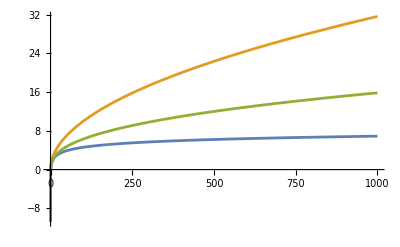

```mathematica
Plot[{Log[x],x^(1/2),x^(2/5)},{x,0,1000}]
```